This project first explores the use of SK combinators to perform arithmetic operations on Church numerals. The project determines their size and time complexity and verifies their optimality through various ways. Several efficient combinators are also found. The project then proposes a new method to construct SK combinators for binary representations of arbitrary length efficiently and bitwise operations. At the end, the project compares their efficiency and the performance to do basic arithmetic.

## Introduction

### SKI and SK Combinators

The SKI combinator calculus is a computational system that was introduced by Moses Schönfinkel and Haskell Curry in the early 20th century (SKI Combinator Calculus). It is important in the study of theoretical computer science as it is proven to be Turing complete, meaning it can perform any calculation with unlimited time and memory. The SKI combinator calculus is made of three combinators, S, K, and I, that can be defined in lambda expressions as follows:

S = λx.λy.λz.xz(yz)
		K = λx.λy.x
		I = λx.x

The S combinator takes three parameters and applies the first two to the third. The K combinator takes two parameters and returns only its first. The I combinator returns the only parameter itself.

The SK combinator calculus, on the other hand, is a reduced version of the SKI combinator calculus, where it is proven that the I combinator can be represented in only S and K combinators, meaning that S and K combinators are a minimal complete set and they can represent any lambda expression. It is a programming language with only two letters. Here is how it works:

S K K x = K x (K x) = x = I x
		I = S K K

Combinators S and K are two built in symbols in the Wolfram Language:

```mathematica
CombinatorS
```

```mathematica
CombinatorK
```

In the Wolfram Language, we can evaluate an SK combinator by repeatedly replacing S and K combinators with their rules.

Functions to evaluate SK combinators:

```mathematica
combinatorRules = {CombinatorS[x_][y_][z_] -> x[z][y[z]], CombinatorK[x_][y_] -> x};
combinatorEvaluate[f_] := f //. combinatorRules
combinatorReplace[f_] := f /. combinatorRules
```

The function combinatorReplace is to replace rules by only once, whereas the function combinatorEvaluate will keep replacing rules until reach the fix point.

An example for the combinator I that is represented in terms of SK combinators:

```mathematica
combinatorEvaluate[[][][x]]
```

x

To convert a lambda expression to SK combinators, the resource function SKCombinatorCompile can be used:

Function to compile a combinator:

```mathematica
combinatorCompile[arg_, f_] := ResourceFunction["SKCombinatorCompile"][f, arg]
```

The first parameter includes a list of parameters, and the second parameter is the body part of the lambda expression.

Examples:

λa.λb.λc.c (a b)

```mathematica
combinatorCompile[{a,b,c},c[a[b]]]
```

[[[[[[][]]]]]][[[]]]

λa.λb.λc.c (a (λd d c b))

```mathematica
combinatorCompile[{a,b,c},c[a[combinatorCompile[{d}, d[c][b]]]]]
```

[[[[[[][]]]]]][[[[]][[[]][[[]][]]]][[[[[[[]][[[[[][]]]][]]]]][[[]][]]]]]

### Church Numerals

Church numerals are representations of natural numbers using lambda notation. The function that represents the Church numeral of any natural number  applies a function  to an initial values   times as follows:

For example:
-Graphics-

In the Wolfram Language, we can nestedly apply a function f to a value x by using the function Nest:

```mathematica
Nest[f,x,5]
```

f[f[f[f[f[x]]]]]

Functions to convert an integer to a church numeral and to convert it back:

```mathematica
intToChurch[n_] := Nest[successor, zero, n]
churchToInt[f_] := Depth[f]-1
```

The definition of successor and zero, which are also represented by SK combinators, will be elaborated later in the section of Previous Works.

The Church numeral serves as a common way to represent natural numbers in lambda calculus, as well as SK combinator calculus. However, it has constraints of being difficult to perform bitwise operations because getting each of its digits in binary is largely inefficient since it involves division and modulus. However, a binary number system might be a more efficient numeral system to perform bitwise operations.

### Binary Number System

#### Binary Representation

All computations by our computers are done in the binary number system. It is a numeral system that is expressed in the base of 2, such that each digit is eighter 1 or 0. Binary numbers of n digits can represent  different numbers from  to 2^n-1. For example, numbers in decimal, which are in the base of 10, can be converted to binary numbers of 3 digits as follows:
-Graphics-

#### Binary Conversion

To convert a decimal number to the binary form, we need to get the value of each of its digits from the first digit (the right most digit) in the binary form. The first digit is the value of the decimal number mod  2. To get following digits, we need to divide the number by 2 and only keep the integer part. We do the same steps until the decimal number equals zero. For example:
-Graphics-

To convert a binary number back to the decimal form, we only need to sum up the 2^i of each digit that is 1, where i its a zero index for its digit from the right most. For example:
-Graphics-

Bitwise operations can be easy to perform in a binary number system because it is mainly about the values of each digit in binary. Several bitwise operations are and, or, xor, nand, and so on. It is proven that nand is a minimal complete set, which can represent any bitwise operation.

## Previous works

### Church Numerals, Successor, and Zero

#### Church Numerals and Successor

The successor is a term in mathematics that is most commonly used for the series and sequence of whole numbers. The successor of a whole number gives its next number, which usually means by adding 1.

In the definition of Church numerals, we know that a church numeral not only represents a natural number , it also functionally means to nestedly apply a function   times to an initial value . We want it to universally work for any function  and initial value . To do this, the lambda expression for a Church numeral takes two parameters  and .

n = λf.λx.f(f(...(f x)))

Using this property,we can depict the lambda expression for a successor of a Church numeral :

succ = λn.λf.λx.f(n f x)

In this lambda expression, the successor takes three parameters, the Church number , the  function , and a value  that the function  applies to. Let’s first see the expression in the parentheses. It means to applies the function  to the   n times. After that, another  applies to it, which serves to increase by one.

Note that the lambda expression below is wrong:

succ = λn.λf.λx.f n

This is the lambda expression I initially thought for successor; however, I later note that it is wrong because according to the lambda expression of the Church numeral , it takes two parameters to “decode.” This clever design that a Church numeral isn’t decoded until it is being used can efficiently help us compile any SK combinator for operations based on it. I also used this method later to construct the binary representation.

Compile the combinator for successor:

```mathematica
successor = combinatorCompile[{n,f,x},f[n[f][x]]]
```

[[[]][]]

Note that there are always infinitely many SK combinators that will point to the same lambda expression. This way of compiling doesn’t guarantee that the size of the SK combinator it compiles will be the smallest. However, the SK combinator above for the successor is verified to be the smallest in the next section.

#### Zero

Zero means the Church numeral of zero. It also takes two parameters like any other Church numeral; however, as it applies the function  zero times to the initial value , it always purely returns the second parameter .

Compile the combinator for zero:

```mathematica
zero = combinatorCompile[{f,x},x]
```

[[][]]

However, this SK combinator is not the smallest. The smallest SK combinator for the zero of the Church numeral is:

```mathematica
zero = [];
```

We can verify its lambda expression through the following evaluation:

```mathematica
combinatorEvaluate[zero[f][x]]
```

x

### SK Combinators for Arithmetic Operations

#### Addition, Multiplication, and Exponentiation

The following SK combinators for addition, multiplication, and exponentiation were found by Stephen Wolfram in his book Combinators: A Centennial View.

```mathematica
plus = [[]][[[[[]][]]]];
times = [[]][];
power = [[[[][]]]][];
```

Examples:

```mathematica
churchToInt[combinatorEvaluate[plus[intToChurch[3]][intToChurch[4]][s][k]]]
```

7

```mathematica
churchToInt[combinatorEvaluate[times[intToChurch[2]][intToChurch[5]][s][k]]]
```

10

```mathematica
churchToInt[combinatorEvaluate[power[intToChurch[3]][intToChurch[2]][s][k]]]
```

9

Their optimality will be verified in the next section.

### Boolean SK Combinators

The reason we need SK combinators for Boolean logic is to perform some conditional logic computations by using SK combinators. To build these logic operations, we need to first define the two most important logic units, true and false in SK combinators. We usually use true and false in an if statement, such as:

```mathematica
If[True,a,b]
```

a

and

```mathematica
If[False,a,b]
```

b

The use of true will always take the first value, whereas false takes the second.

Let’s define the lambda expression for the function if, first, and second to be:

if = λp.λa.λb.p a b
		first = λa.λb.a
		second = λa.λb.b

According to the lambda expressions, we then can get their SK combinators through compiling:

```mathematica
if = combinatorCompile[{p,a,b},p[a][b]]
first = combinatorCompile[{a,b},a]
second = combinatorCompile[{a,b},b]
```

[][]

[[][]]

Their shortest SK combinators:

```mathematica
if = [][];
first = ;
second = [];
```

Note that you can understand First as True, and Second as False.

Stephen Wolfram has found the minimal SK combinators for all bitwise operations of length up to one by search (Wolfram):

15 | -Graphics- | True | k[k[k]] | ()
14 | -Graphics- | Or | s[s[s]][s][s[k]] | ()()
13 | -Graphics- |  | s[k[s[s[s][k[k[k]]]]]][k] | ((((()))))
12 | -Graphics- | First | k | 
11 | -Graphics- | Implies | s[s][k[k[k]]] | (())
10 | -Graphics- | Last | s[k] | 
9 | -Graphics- | Equal | s[s][k[s[s[s][k[k[k]]]][s]]] | ((((()))))
8 | -Graphics- | And | s[s][k] | 
7 | -Graphics- | Nand | s[s[k[s[s[s][k[k[k]]]]]]][s] | (((((())))))
6 | -Graphics- | Xor | s[s[s[s[s]][s[s[s[k]]]][s]]][k] | ((()((()))))
5 | -Graphics- | Not | k[s[s[s][k[k[k]]]][s]] | (((())))
4 | -Graphics- |  | s[k[s[s[s[s[k]]][s]]]][k] | ((((()))))
3 | -Graphics- | Not | s[s][s[s[s[s[k]]][s]]][k[k]] | (((())))()
2 | -Graphics- |  | s[s[s[k]]][s] | (())
1 | -Graphics- | Nor | s[s[s[s[s][k[k[k[k]]]]]][k[s]]] | (((((()))))())
0 | -Graphics- | False | k[k[s[k]]] | (())

In addition to finding these SK combinators for bitwise operations of length of one through search, we can also construct them by compiling.

Compile the SK combinator for the xor operation of length of one:

```mathematica
xor=combinatorCompile[{a,b},a[b[first][second]][b[first][second]]]
```

[[[]][[[[]][]][[[[[][]][[]]][[[]]]]]]][[[[[][]][[]]][[[]]]]]

This expression is like a nested if statement where if both parameters are true or both of them are false, which goes to either the first or the fourth case, it returns false, otherwise it returns true.

Simplify the combinator by replacing b[true][false] with b:

```mathematica
xor=combinatorCompile[{a,b},a[b[second][first]][b]]
```

[[[]][[[[]][]][[[[[][]][[[]]]][[]]]]]][[[][]]]

For example, this code returns the combinator K, which stands for the false:

```mathematica
combinatorEvaluate[xor[first][second]]
```

We can utilize the idea to construct binary representation by first constructing its logic units true and false and this way to compile through nested if statement in the later part of this essay to construct the binary representation of any length.

## Finding Optimal Combinator Representations for Arithmetic

My initial research question was finding optimal combinator representations for arithmetic (addition, multiplication, and exponentiation) with different ways to represent integers. However, I was able to verify through brute force that Wolfram’s expressions are already minimal much quicker than expected, and expressions for arithmetic operations are independent of the successor function (will later be elaborated). However, I still found several other efficient combinator representations for arithmetic.

We can find other SK combinators that can also do these arithmetic operations through different ways.

Before starting, to test the optimality of a combinator, we need to take views from two aspects, its size and its number of steps to the fix points. Usually, the smallest the size, the less steps to the fix point; however, this is not always true. That is why we need to try different methods rather than just brute force.

Functions to return the size of a combinator and the number of steps to its fixed point

```mathematica
combinatorSize[comb_] := LeafCount[comb]
stepsToFixPoint[comb_] := Length[ResourceFunction["CombinatorFixedPointList"][comb]]
```

### Direct Compiling

Let’s first try to directly compile each of arithmetic operations

#### Addition

Given that the lambda expression for addition is:

plus = λm.λn.λf.λx.m f (n f x)

Compile its combinator according to the lambda expression:

```mathematica
combinatorCompile[{m,n,f,x},m[f][n[f][x]]]
```

[[]][[[[[]]]][[[]]]]

This plus combinator has a size of 10, which is one unit longer than the one in Stephen Wolfram’s book.

#### Multiplication

The lambda expression for multiplication is:

times = λm.λn.λf.λx.m (n f) x

Compile its combinator according to the lambda expression:

```mathematica
combinatorCompile[{m,n,f,x},m[n[f]][x]]
```

[[]][]

Simplify the expression:

```mathematica
combinatorCompile[{m,n,f},m[n[f]]]
```

[[]][]

It gives the same SK combinator as the one Stephen Wolfram found in his book.

#### Exponentiation

The lambda expression for exponentiation is:

power = λm.λn.λf.λx.(n m) f x

Compile its combinator according to the lambda expression

```mathematica
combinatorCompile[{m,n,f,x},n[m][f][x]]
```

[[[[][]]]][]

Simplify the expression

```mathematica
combinatorCompile[{m,n},n[m]]
```

[[[[][]]]][]

It also gives the same SK combinator as the one Stephen Wolfram found in his book.

### Brute Force Enumeration

We can brute forcibly enumerate all SK combinators smaller than or equal to the size of each arithmetic SK combinator to verify the optimality of the current ones.

We can generate all combinations of SK combinators of a given size n through recursion:

```mathematica
ClearAll[{combinatorEnumerate}];
combinatorEnumerate[1] = {CombinatorS, CombinatorK};
combinatorEnumerate[n_] := combinatorEnumerate[n] = Flatten[
      Table[
        Module[{pre = combinatorEnumerate[i], end = combinatorEnumerate[n - i]},
          Table[x[y], {x, pre}, {y, end}]
          ],
        {i, 1, n - 1}]
        ]
```

Here, I applied the DFS memorization so that for each n, find[n] will only be computed at most once, largely speed up the code.

Or, you can enumerate combinators by the resource function EnumerateCombinators:

```mathematica
combinatorEnumerate[n_] := ResourceFunction["EnumerateCombinators"][n];
```

Building a graph for the relationships between combinators, we create a directed edge if one combinator can transfer to another by applying the rules once. Since one combinator can transfer to different combinators by changing the order of applying rules, and the multiple different combinators can lead to a same final expression or the fix point, the relationship between combinators is a DAG graph (directed acyclic graph) rather than a tree. For any two combinators, if they are connected by a road or path, they are equivalent, and for any combinator, there are infinite equivalent combinators as you can keep replacing the rule of combinator K on it. In some rare cases, their relationships aren’t a DAG graph but can form cycle. In this situation, the combinator has no fixed point and its evaluation will never halt.

Function to find SK combinators equivalent to a given lambda expression:

```mathematica
combinatorMatch[comb_, arg_, expr_, steps_:20] := DeleteDuplicates[
 Select[comb, 
  MatchQ[expr, Nest[combinatorReplace, Fold[#[#2]&,#,arg], steps]] &]]
```

This function deletes equivalent combinators, such one that is another’s ancestor (lead to a same combinator during the evaluation process). To avoid infinite evaluation, we set the parameter steps to perform a fix number of replacement; however, this might miss some potential combinators that also work.

Since the number of SK combinators increases exponentially, we only want to check combinators of size 9 or less.

#### Addition

The current minimal addition combinator has a size of 9. Let’s enumerate all SK combinator with the size of 9 or less.

```mathematica
combinatorMatch[Flatten[combinatorEnumerate[#]&/@Range[1,9]],{m,n,f,x},m[f][n[f][x]]]
```

{[[]][[[[[]][]]]]}

It is shown that the only SK combinator with size 9 or less is the one Stephen Wolfram found, showcasing its minimality.

#### Multiplication

Within the size of 5, there is only one combinator for multiplication, showing its minimality.

```mathematica
combinatorMatch[Flatten[combinatorEnumerate[#]&/@Range[1,5]],{m,n,f,x},m[n[f]][x]]
```

{[[]][]}

However, within the range of 6, there are 17 combinators for multiplication.

```mathematica
combinatorMatch[Flatten[combinatorEnumerate[#]&/@Range[1,6]],{m,n,f,x},m[n[f]][x]]
```

{[[]][],[][[]][[]],[[]][][][],[[]][[][]],[[]][[][]],[[][][]][],[[[][]]][],[[[]][]][],[[[][]]][],[[[]][]][],[[][][]][],[][][[]][],[[[]]][][],[[[]][]][],[[[]][]][],[[[]]][][],[][][[]][]}

It’s interesting to consider how will the number of combinators will grow as the size get bigger.

Visualize the distribution of combinators for multiplication:

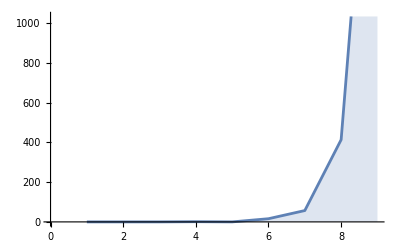

```mathematica
ListLinePlot[Table[Length[combinatorMatch[combinatorEnumerate[i],{m,n,f,x},m[n[f]][x]]],{i,1,9}], Filling->Axis]
```

The number of combinators for multiplication increases exponentially as the size increases. An exception happens at the size of 4 to 5, which decreases a bit.

#### Exponentiation

The current minimal exponentiation combinator has a size of 7. Let’s enumerate all SK combinator with the size of 7 or less.

```mathematica
powerCombinatorList = combinatorMatch[Flatten[combinatorEnumerate[#]&/@Range[1,7]],{m,n,f,x},n[m][f][x]]
```

{[[[]][[]]][],[[[[[]]]]][],[[[[][]]]][],[[[[][]]]][]}

There are four combinators of size 7 for exponentiation. Let’s compare their efficiency to the fixed point:

```mathematica
Grid[Table[{x,stepsToFixPoint[x[a][b][s][k]]},{x,powerCombinatorList}]]
```

[[[]][[]]][] | 8
[[[[[]]]]][] | 8
[[[[][]]]][] | 7
[[[[][]]]][] | 7

It is found that there exists another combinator for exponentiation of the same size and efficiency.

Visualize the distribution of combinators for multiplication

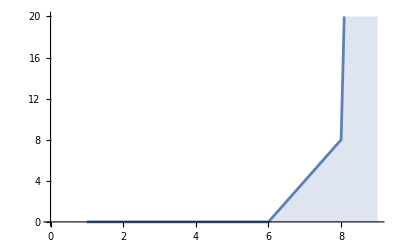

```mathematica
ListLinePlot[Table[Length[combinatorMatch[combinatorEnumerate[i],{m,n,f,x},n[m][f][x]]],{i,1,9}], Filling->Axis]
```

The number of exponentiation combinators increases dramatically when the size is 8 to 9.

### Compiling Addition from Successor

Finding smaller combinators through enumeration shows that the current one is already minimal with the lambda expression for addition. I tried to compile addition with an alternative lambda expression for addition that is based on successor, which I hope can find shorter combinators in this way.

#### Addition’s Successor-based Lambda Expression

The nature of addition is to apply successor a number of times to a number. For example, 2+3 means to apply successor to 3 twice. We can therefore have the lambda expression for the addition based on any successor:

plus = λn.λm.n succ m

Function to compile the SK combinator for addition given any successor:

```mathematica
plusCombinator[succ_] := combinatorCompile[{a,b},a[succ][b]]
```

Let’s try to compile the SK combinator for addition with the current successor:

```mathematica
plusCombinator[successor]
```

[[][]][[[[[]][]]]]

It is shown that this plus combinator has a size of 10, which is slightly longer than the current plus combinator of size 9.

#### Brute Forcibly Find Successors

```mathematica
combinatorMatch[Flatten[combinatorEnumerate[#]&/@Range[1,5]],{n,f,x},f[n[f][x]]]
```

{[[[]][]]}

For the size of 5 or less, there is only one successor, which is the one that we already know.

```mathematica
combinatorMatch[Flatten[combinatorEnumerate[#]&/@Range[1,6]],{n,f,x},f[n[f][x]]]
```

{[[[]][]],[[]][][][],[][][[]][]}

When checking the size of 6 or less, there are three.

Visualize the distribution of successor combinator by size:

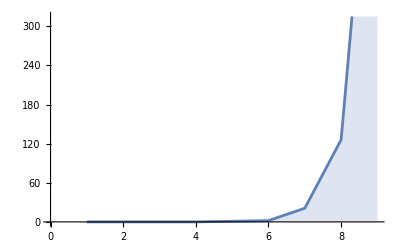

```mathematica
ListLinePlot[Table[Length[combinatorMatch[combinatorEnumerate[i],{n,f,x},f[n[f][x]]]],{i,1,9}], Filling->Axis]
```

To see if the longer successor can compile shorter addition combinators, we enumerate the sizes of all combinators for addition for successor’s of size from 5 to 8.

```mathematica
Column[Table[Table[combinatorSize[plusCombinator[x]],{x,combinatorMatch[combinatorEnumerate[i],{n,f,x},f[n[f][x]]]}],{i,5,8}]]
```

{10}
{11,11}
{12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12}
{13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13}

We find that the size of addition is exactly the size of its successor plus 5. This can be proven by replacing the successor in the lambda expression with an undefined variable c:

```mathematica
combinatorCompile[{a,b},a[c][b]]
```

[[][]][[c]]

It always nests the successor’s combinator into the same combinator of size of 5, which explains the pattern above.

This shows the way to find addition’s combinator based on successor doesn’t give smaller combinators for addition. This is because the lambda expression for addition and the lambda expression for addition that is based on a give successor are homologous, which means if you substitute the lambda expression for successor into the expression for addition based on a successor, it is equivalent to the other.

### Commutative Law

Addition and multiplication are commutative, which means that we are able to swap the position of two parameters and the result won’t change. For exponentiation, although it doesn’t hold the law, we can also try to swap its parameters during compiling, since the order of parameters of a function can be flexible when you call the function.

Compile addition with swapped parameters:

```mathematica
combinatorCompile[{m,n,f,x},n[f][m[f][x]]]
```

[[[[[]][[[[[]]]][[[]]]]]]][]

Compile multiplication with swapped parameters:

```mathematica
combinatorCompile[{m,n,f},n[m[f]]]
```

[[[[[]][]]]][]

Compile exponentiation with swapped parameters:

```mathematica
combinatorCompile[{m,n},m[n]]
```

[][]

For addition and multiplication, their returned combinators are longer than the current one; however, for exponentiation, the one it compiles, which has only size of 3, is much smaller than the one before, which has size of 7. Also, we notice that the combinator compiled with swapped parameter for exponentiation is same as the SK combinator representation for the combinator I, which returns the parameter itself.

The result that combinators for exponentiation but not addition and multiplication with swapped parameters is shorter makes sense because the order of variables in the expression is exactly same as the order of parameters, whereas the addition and multiplication gets more disordered.

### Efficiency Comparison

We can compare the efficiency (number of steps to  evaluate) between the arithmetic combinator Stephen Wolfram found and those I found. We will compare their efficiency by tabling and graphing their evolution. We only compare those combinators that have size close to the minimal size.

#### Addition

The three addition combinators that we are going to test:

```mathematica
Column[plusCombinatorList = {[[]][[[[[]][]]]], [[][]][[[[[]][]]]], [[]][[[[[]]]][[[]]]]}]
```

[[]][[[[[]][]]]]
[[][]][[[[[]][]]]]
[[]][[[[[]]]][[[]]]]

To make the combinator fully evaluated, we need to substitute two Church numerals as parameters instead of a and b.

Substitute 2 and 3:

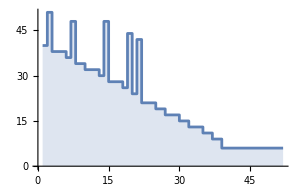
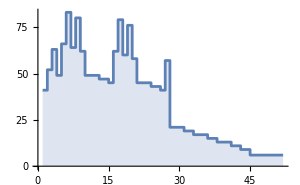
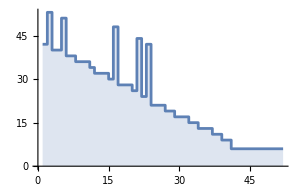

```mathematica
Row[Table[ListStepPlot[
 combinatorSize /@ 
  ResourceFunction["CombinatorEvolveList"][comb[intToChurch[2]][intToChurch[3]][][],50], Filling -> Axis, ImageSize -> 300],{comb,plusCombinatorList}], "     "]
```

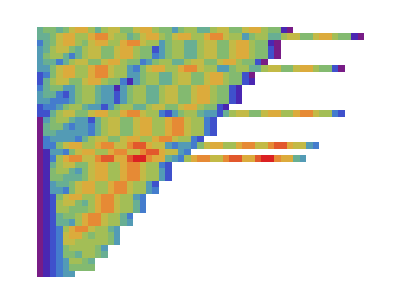
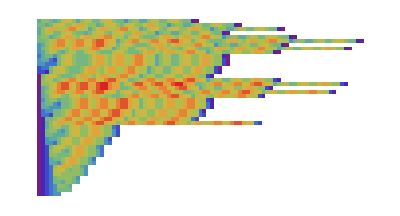
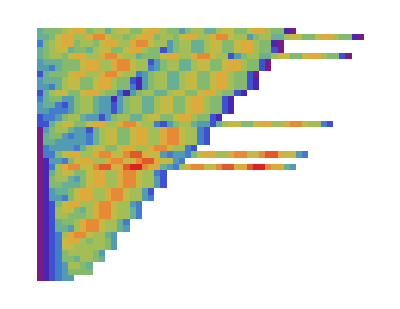

```mathematica
Magnify[Row[Table[ResourceFunction["CombinatorEvolutionPlot"][ResourceFunction["CombinatorFixedPointList"][comb[intToChurch[2]][intToChurch[3]][][]],"ExpressionDepthPlot"],{comb,plusCombinatorList}],"     "],2.5]
```

The first combinator, the one Stephen Wolfram found, arrives at the fixed point in 39 steps, the second one in 45, and the third one in 41.

Substitute 3 and 2:

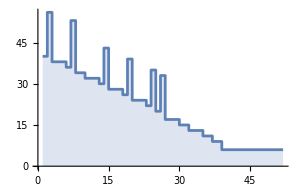
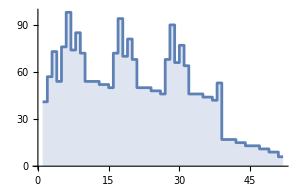
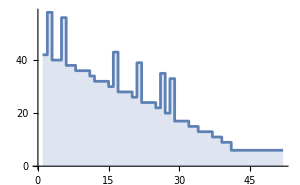

```mathematica
Row[Table[ListStepPlot[
 combinatorSize /@ 
  ResourceFunction["CombinatorEvolveList"][comb[intToChurch[3]][intToChurch[2]][][],50], Filling -> Axis, ImageSize -> 300],{comb,plusCombinatorList}],"     "]
```

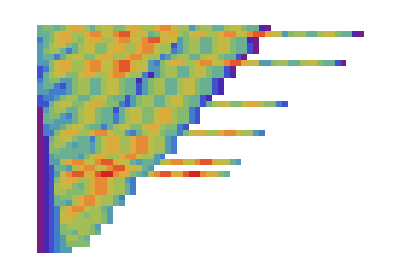
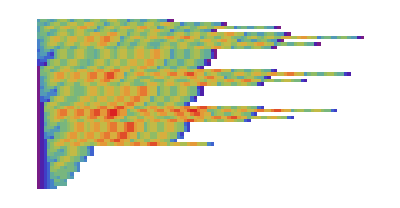
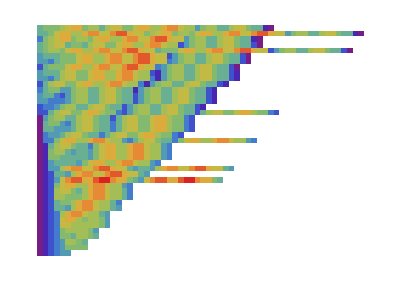

```mathematica
Magnify[Row[Table[ResourceFunction["CombinatorEvolutionPlot"][ResourceFunction["CombinatorFixedPointList"][comb[intToChurch[3]][intToChurch[2]][][]],"ExpressionDepthPlot"],{comb,plusCombinatorList}],"     "],2.5]
```

The first combinator arrives at the fixed point in 39 steps, the second one in 51, and the third one in 41. This means that the order of parameters matters for the second addition combinator but not the first and third.

Substitute 7 and 8:

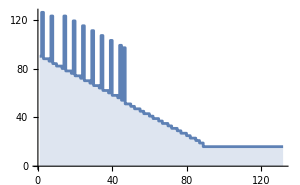
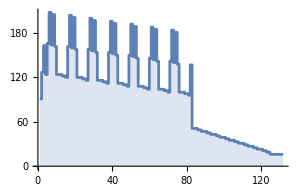
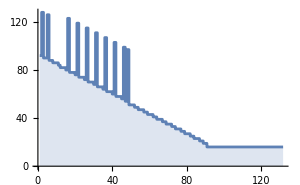

```mathematica
Row[Table[ListStepPlot[
 combinatorSize /@ 
  ResourceFunction["CombinatorEvolveList"][comb[intToChurch[7]][intToChurch[8]][][],130], Filling -> Axis, ImageSize -> 300],{comb,plusCombinatorList}],"     "]
```

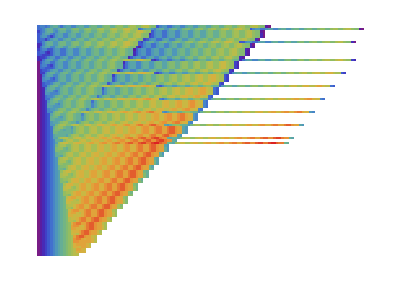
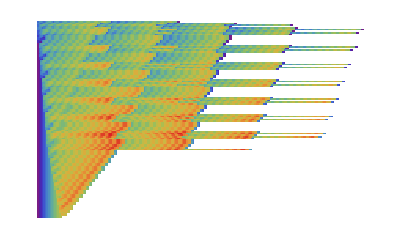
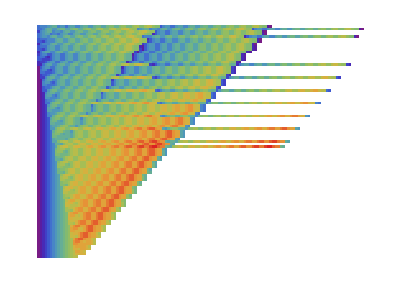

```mathematica
Magnify[Row[Table[ResourceFunction["CombinatorEvolutionPlot"][ResourceFunction["CombinatorFixedPointList"][comb[intToChurch[7]][intToChurch[8]][][]],"ExpressionDepthPlot"],{comb,plusCombinatorList}],"     "],2.5]
```

The first combinator arrives at the fixed point in 89 steps, the second one in 125, and the third one in 91.

The gap of number of steps between the second one and the first and the third one significantly increases. This implies that the number of steps to reach the fixed point for one or more of these combinators might not be constant or linear. We can create tables to observe the pattern.

```mathematica
Row[Table[Grid[Table[stepsToFixPoint[comb[intToChurch[a]][intToChurch[b]][][]],{a,1,10},{b,1,10}],Frame->All],{comb,plusCombinatorList}],"     "]
```

24 | 29 | 34 | 39 | 44 | 49 | 54 | 59 | 64 | 69
29 | 34 | 39 | 44 | 49 | 54 | 59 | 64 | 69 | 74
34 | 39 | 44 | 49 | 54 | 59 | 64 | 69 | 74 | 79
39 | 44 | 49 | 54 | 59 | 64 | 69 | 74 | 79 | 84
44 | 49 | 54 | 59 | 64 | 69 | 74 | 79 | 84 | 89
49 | 54 | 59 | 64 | 69 | 74 | 79 | 84 | 89 | 94
54 | 59 | 64 | 69 | 74 | 79 | 84 | 89 | 94 | 99
59 | 64 | 69 | 74 | 79 | 84 | 89 | 94 | 99 | 104
64 | 69 | 74 | 79 | 84 | 89 | 94 | 99 | 104 | 109
69 | 74 | 79 | 84 | 89 | 94 | 99 | 104 | 109 | 11424 | 29 | 34 | 39 | 44 | 49 | 54 | 59 | 64 | 69
35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80
46 | 51 | 56 | 61 | 66 | 71 | 76 | 81 | 86 | 91
57 | 62 | 67 | 72 | 77 | 82 | 87 | 92 | 97 | 102
68 | 73 | 78 | 83 | 88 | 93 | 98 | 103 | 108 | 113
79 | 84 | 89 | 94 | 99 | 104 | 109 | 114 | 119 | 124
90 | 95 | 100 | 105 | 110 | 115 | 120 | 125 | 130 | 135
101 | 106 | 111 | 116 | 121 | 126 | 131 | 136 | 141 | 146
112 | 117 | 122 | 127 | 132 | 137 | 142 | 147 | 152 | 157
123 | 128 | 133 | 138 | 143 | 148 | 153 | 158 | 163 | 16826 | 31 | 36 | 41 | 46 | 51 | 56 | 61 | 66 | 71
31 | 36 | 41 | 46 | 51 | 56 | 61 | 66 | 71 | 76
36 | 41 | 46 | 51 | 56 | 61 | 66 | 71 | 76 | 81
41 | 46 | 51 | 56 | 61 | 66 | 71 | 76 | 81 | 86
46 | 51 | 56 | 61 | 66 | 71 | 76 | 81 | 86 | 91
51 | 56 | 61 | 66 | 71 | 76 | 81 | 86 | 91 | 96
56 | 61 | 66 | 71 | 76 | 81 | 86 | 91 | 96 | 101
61 | 66 | 71 | 76 | 81 | 86 | 91 | 96 | 101 | 106
66 | 71 | 76 | 81 | 86 | 91 | 96 | 101 | 106 | 111
71 | 76 | 81 | 86 | 91 | 96 | 101 | 106 | 111 | 116

For each combinator, we subtract the number of steps to evaluate Church numerals from the total steps. This can ensure that we only compare the number of steps for the addition combinators themselves.

```mathematica
Row[Table[Grid[Table[stepsToFixPoint[comb[intToChurch[a]][intToChurch[b]][][]]-stepsToFixPoint[intToChurch[a][][]]-stepsToFixPoint[intToChurch[b][][]],{a,1,10},{b,1,10}],Frame->All],{comb,plusCombinatorList}],"     "]
```

8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 88 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14
20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20
26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26 | 26
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32
38 | 38 | 38 | 38 | 38 | 38 | 38 | 38 | 38 | 38
44 | 44 | 44 | 44 | 44 | 44 | 44 | 44 | 44 | 44
50 | 50 | 50 | 50 | 50 | 50 | 50 | 50 | 50 | 50
56 | 56 | 56 | 56 | 56 | 56 | 56 | 56 | 56 | 56
62 | 62 | 62 | 62 | 62 | 62 | 62 | 62 | 62 | 6210 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10

We find that the first and third combinators always have a constant number of steps to the fixed point. For the second combinator, it shows a linear increasing efficiency: the second addend doesn’t impact the efficiency; however, as the first addend increases by 1, the total number of steps to the fixed point increases by 6.

Using ListPointPlot3D to visualize the steps to the fixed point in 3D:

```mathematica
Row[Table[ListPointPlot3D[Table[stepsToFixPoint[comb[intToChurch[a]][intToChurch[b]][][]]-stepsToFixPoint[intToChurch[a][][]]-stepsToFixPoint[intToChurch[b][][]],{a,1,10},{b,1,10}],ColorFunction->"Rainbow", ImageSize->200],{comb,plusCombinatorList}],"     "]
```

-Graphics3D--Graphics3D--Graphics3D-

We can conclude that the first and third plus combinators have a time complexity of O(a+b) with a constant coefficient, where a  and b are its addends.

#### Multiplication

Since all other combinators we found are much bigger than the one Stephen Wolfram found, which has only size of 4, we are going to only test efficiency for this one.

```mathematica
times
```

[[]][]

Tabling the Substitution

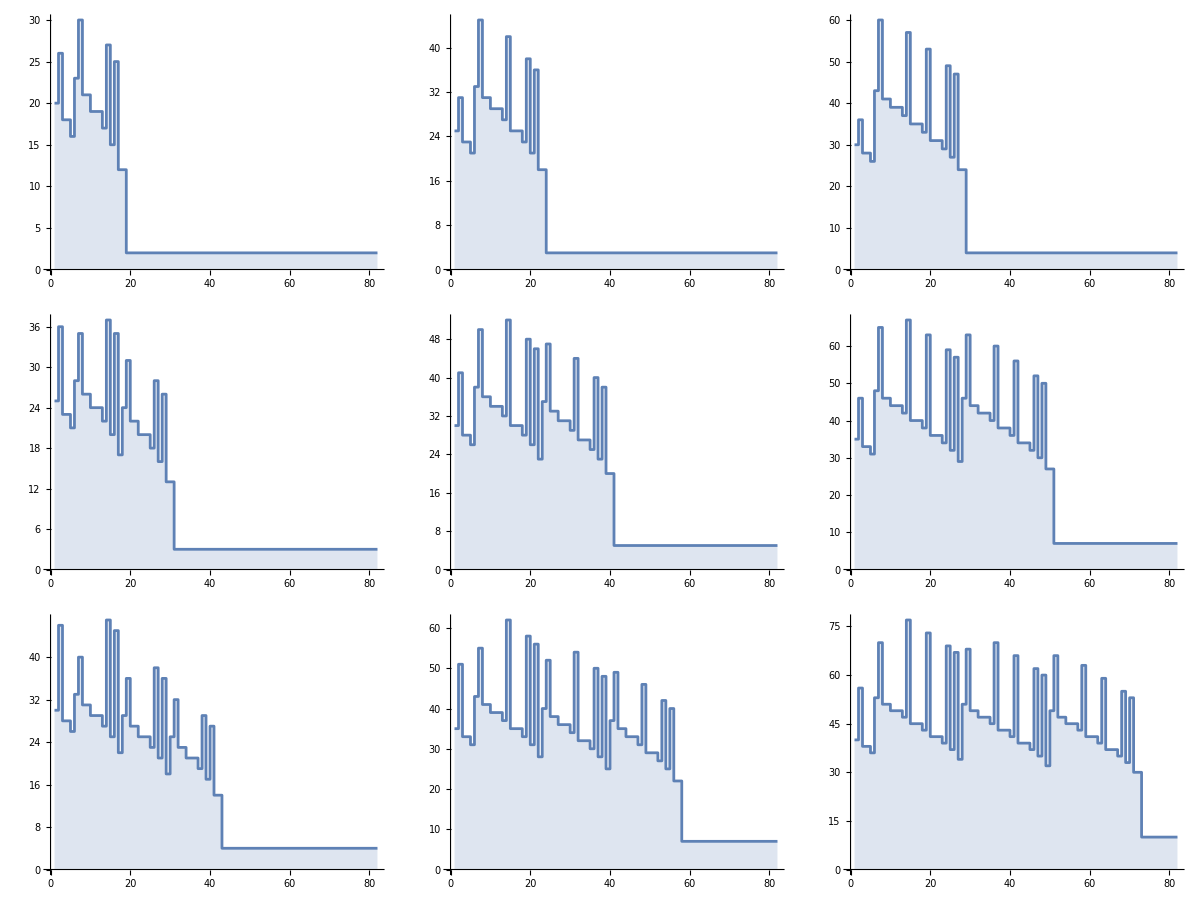

```mathematica
Grid[Table[ListStepPlot[
 combinatorSize /@ 
  ResourceFunction["CombinatorEvolveList"][times[intToChurch[a]][intToChurch[b]][][],80], Filling -> Axis, ImageSize -> 300],{a,1,3},{b,1,3}]]
```

It is not hard to find that for each graph above, its number of peaks is its first addend. For each first-level peak, the number of local peaks is its second addend.

The depths of each expression of the combinator evolution:

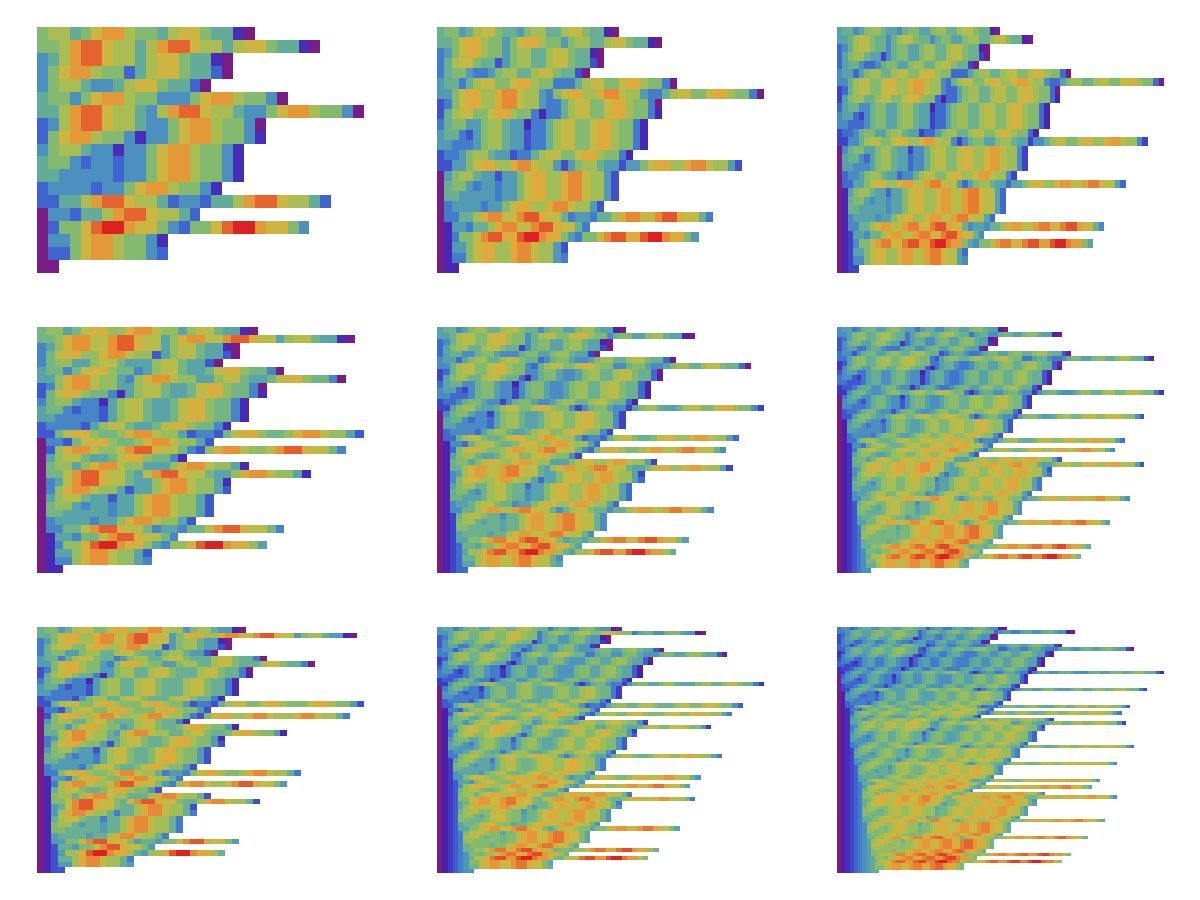

```mathematica
Grid[Table[ResourceFunction["CombinatorEvolutionPlot"][ResourceFunction["CombinatorFixedPointList"][times[intToChurch[a]][intToChurch[b]][][]],"ExpressionDepthPlot"],{a,1,3},{b,1,3}]]
```

Tabling the number of steps to the fixed point:

```mathematica
Grid[Table[stepsToFixPoint[times[intToChurch[a]][intToChurch[b]][][]],{a,1,10},{b,1,10}],Frame->All]
```

19 | 24 | 29 | 34 | 39 | 44 | 49 | 54 | 59 | 64
31 | 41 | 51 | 61 | 71 | 81 | 91 | 101 | 111 | 121
43 | 58 | 73 | 88 | 103 | 118 | 133 | 148 | 163 | 178
55 | 75 | 95 | 115 | 135 | 155 | 175 | 195 | 215 | 235
67 | 92 | 117 | 142 | 167 | 192 | 217 | 242 | 267 | 292
79 | 109 | 139 | 169 | 199 | 229 | 259 | 289 | 319 | 349
91 | 126 | 161 | 196 | 231 | 266 | 301 | 336 | 371 | 406
103 | 143 | 183 | 223 | 263 | 303 | 343 | 383 | 423 | 463
115 | 160 | 205 | 250 | 295 | 340 | 385 | 430 | 475 | 520
127 | 177 | 227 | 277 | 327 | 377 | 427 | 477 | 527 | 577

This time, instead of subtracting from, we divide the number of steps by the multiplier and multiplicand:

```mathematica
Grid[Table[Round[stepsToFixPoint[times[intToChurch[a]][intToChurch[b]][CombinatorS][CombinatorK]]/a/b],{a,1,10},{b,1,10}],Frame->All]
```

19 | 12 | 10 | 8 | 8 | 7 | 7 | 7 | 7 | 6
16 | 10 | 8 | 8 | 7 | 7 | 6 | 6 | 6 | 6
14 | 10 | 8 | 7 | 7 | 7 | 6 | 6 | 6 | 6
14 | 9 | 8 | 7 | 7 | 6 | 6 | 6 | 6 | 6
13 | 9 | 8 | 7 | 7 | 6 | 6 | 6 | 6 | 6
13 | 9 | 8 | 7 | 7 | 6 | 6 | 6 | 6 | 6
13 | 9 | 8 | 7 | 7 | 6 | 6 | 6 | 6 | 6
13 | 9 | 8 | 7 | 7 | 6 | 6 | 6 | 6 | 6
13 | 9 | 8 | 7 | 7 | 6 | 6 | 6 | 6 | 6
13 | 9 | 8 | 7 | 7 | 6 | 6 | 6 | 6 | 6

We find that as the multiplier and the multiplicand increases, the number of steps divided by them approaches 6. This implies that it has a time complexity of O(a×b) with a constant coefficient of 6, where a and b are its multiplier and multiplicand.

#### Exponentiation

Adding the one that swaps its parameters:

```mathematica
Column[powerCombinatorList = Append[powerCombinatorList,[][]]]
```

[[[]][[]]][]
[[[[[]]]]][]
[[[[][]]]][]
[[[[][]]]][]
[][]

Substitute 2 and 3:

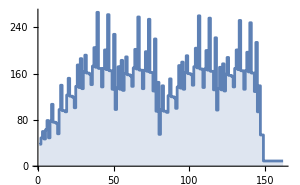
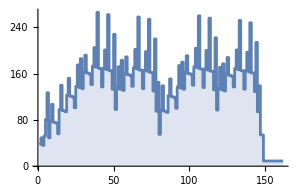
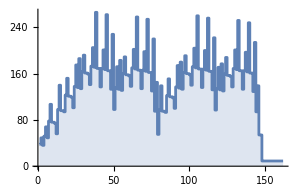
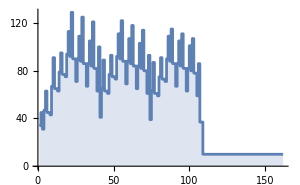
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Table[ListStepPlot[
 combinatorSize /@ 
  ResourceFunction["CombinatorEvolveList"][comb[intToChurch[2]][intToChurch[3]][][],160], Filling -> Axis, ImageSize -> 300],{comb,powerCombinatorList}], "     "]
```

The first two exponentiation combinators take 149 steps, the next two take 148 steps, and the last one takes only 109 steps, which is much less than the others.

This time, there are more nested peaks, and we can assume that they are following the pattern of exponentiation.

The position depths in each expression of the combinator evolution:

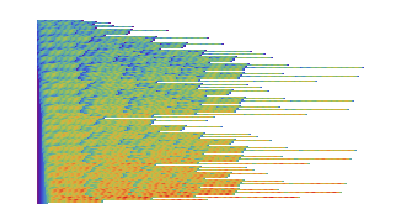
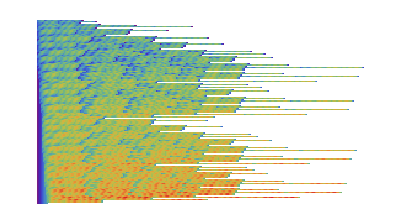
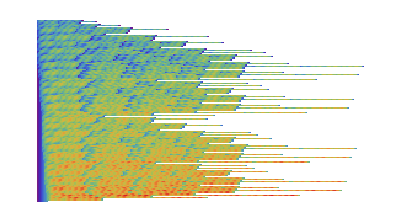
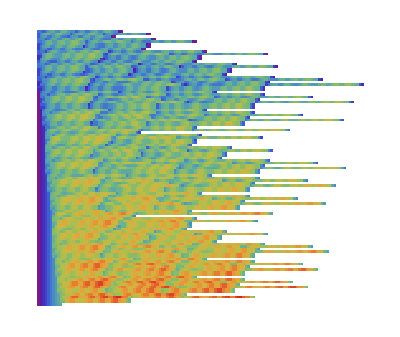
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Magnify[Row[Table[ResourceFunction["CombinatorEvolutionPlot"][ResourceFunction["CombinatorFixedPointList"][comb[intToChurch[2]][intToChurch[3]][][]],"ExpressionDepthPlot"],{comb,powerCombinatorList}],"     "],2.5]
```

Since two pairs look identical, we only keep one from each pair for the following graphing.

```mathematica
Column[powerCombinatorList = {[[[]][[]]][],[[[[][]]]][],[][]}]
```

[[[]][[]]][]
[[[[][]]]][]
[][]

To sum up, for all these three arithmetic operations, addition, multiplication, and exponentiation, they all have linear complexity in the output value, where the number of steps to the fixed point grows proportionally to the magnitude of the result. This is attributed to the nature that all these three operations are built on the successor, which means that each operation builds upon repeated incrementation from an initial value, resulting in the overall complexity scaling linearly with the size of the output.

## Arbitrary-length Binary Representation and Bitwise Operations

In this crucial section of the computational essay, we design and construct arbitrary-length binary representation and bitwise operations using SK combinators. This binary representation can be converted to Church numerals and vice versa. This is significant because it not only enables the execution of bitwise operations but also demonstrates the Turing completeness of SK combinator calculus.

### Binary Representation in SK Combinators

To design arbitrary-length binary representations in SK combinators, it must have two properties. First, it must be constructed with smallest binary units, true and false, for each digit to efficiently perform bitwise operations. Second, we must be able to extract each digit of this binary number. To break down the second point, we design two functions first and second. The function first will always takes the current digit, whereas the function second will remove the current digit and let the second digit be the new first digit. For the smallest units true and false, they must be performed as an if statement, such that:

first = λa.λb.a
		second = λa.λb.b

Therefore, by combining all these together, the full lambda expressions for a binary representation for the outer-most digit being true and for the outer-most digit being false are:

true = λn.λf.λa.λb.f n a
		false = λn.λf.λa.λb.f n b

True and false for each binary digit take four parameters. The first parameter n is the binary numeral without the first digit, which includes all digits from the second to the last. The second parameter is a function f, which is usually first or second. If f is first, it will returns its first argument, which is n, the binary numeral without the first digit; otherwise it returns the third or fourth argument, depending on if it’s true or false.

Compile true and false:

```mathematica
binaryTrue = combinatorCompile[{a,b,c,d},b[a][c]]
binaryFalse = combinatorCompile[{a,b,c,d},b[a][d]]
```

[[[[[[]]]]]][[[[[][]]]][]]

[[[[]]]][[[[[][]]]][]]

Brute forcibly search for minimal true and false:

```mathematica
binaryTrue = combinatorMatch[Flatten[Map[combinatorEnumerate,Range[1,9]]],{a,b,c,d}, b[a][c]][[1]]
binaryFalse = combinatorMatch[Flatten[Map[combinatorEnumerate,Range[1,9]]],{a,b,c,d}, b[a][d]][[1]]
```

```mathematica
binaryTrue = [[[[[[[]]]]]]][];
binaryFalse = [[[[[]]]]][];
```

The full binary numeral of a number follows the rules of binary number system.

Function to convert between binary numerals and integers:

```mathematica
binaryToInt[expr_] := If[MatchQ[, expr], 0, combinatorEvaluate[expr[second][1][0]]+binaryToInt[combinatorEvaluate[expr[first][1][0]]]*2]
intToBinary[x_, d_] := If[MatchQ[0, d], , If[MatchQ[1,Mod[x,2]], binaryTrue, binaryFalse][intToBinary[Floor[x/2], d-1]]]
```

The function intToBinary takes two parameters. The first is the integer you want to convert from, and the second is the length of binary numerals you want after the conversion. Note that if x ≥ 2^d, it will lose information for higher digits.

The full binary numeral of the number 6:

```mathematica
binarySix = binaryFalse[binaryTrue[binaryTrue[]]]
```

[[[[[]]]]][][[[[[[[[]]]]]]][][[[[[[[[]]]]]]][][]]]

Or using the function intToBinary:

```mathematica
binarySix = intToBinary[6,3]
```

[[[[[]]]]][][[[[[[[[]]]]]]][][[[[[[[[]]]]]]][][]]]

To get the first digit of the number 6 in binary, we can have:

```mathematica
combinatorEvaluate[binarySix[second][1][0]]
```

0

To get the binary numeral without the first digit, we can have:

```mathematica
combinatorEvaluate[binarySix[first][1][0]]
```

[[[[[]]]]][[[[[[[]]]]][[]]]]

Convert to the integer:

```mathematica
binaryToInt[combinatorEvaluate[binarySix[first][1][0]]]
```

3

### Bitwise Operations in SK Combinators

The way we construct SK combinators is recursion. We create a function to compile n-digit binary numerals. In the first level of the recursion, we can get its first digit. Since each digit is like a true or false, which has the property that behaves like first or second, we can have its result in different cases.

#### Not

Compile the bitwise operation for not (reverse each digit):

```mathematica
binaryNot[0] := combinatorCompile[{a}, ]
binaryNot[n_] := combinatorCompile[{a}, a[second][binaryFalse][binaryTrue][binaryNot[n-1][a[first][CombinatorS][CombinatorK]]]]
```

In this case, the compiler first gets the first binary digit by following a with [second][binaryFalse][binaryTrue], so that it gives binary false if the digit is binary true, otherwise binary true. Then, by the definition of the binary numeral, it recursively compiles a not combinator for the binary numeral without the first digit by following a with [first][CombinatorS][CombinatorK]. Note that the content in the last two parameters is irrelevant.

Example:

```mathematica
binaryToInt[combinatorEvaluate[binaryNot[3][intToBinary[6,3]]]]
```

1

#### And

Compile the bitwise operation for and:

```mathematica
binaryAnd[0] := combinatorCompile[{a, b}, ]
binaryAnd[d_] := combinatorCompile[{a, b}, a[second][b[second][binaryTrue][binaryFalse]][binaryFalse][binaryAnd[d-1][a[first][CombinatorS][CombinatorK]][b[first][CombinatorS][CombinatorK]]]]
```

In this case, we separate it into three cases. If the digit of a is true and the digit of b is also true, it returns true. If the digit of a is true and the digit of b is false, it returns false. If the digit of a is false, it returns false. After that, it just continues the recursion.

Example:

```mathematica
binaryToInt[combinatorEvaluate[binaryAnd[3][intToBinary[5,3]][intToBinary[6,3]]]]
```

4

#### Or

Compile the bitwise operation for or:

```mathematica
binaryOr[0] := combinatorCompile[{a, b}, ]
binaryOr[d_] := combinatorCompile[{a, b}, a[second][binaryTrue][b[second][binaryTrue][binaryFalse]][binaryOr[d-1][a[first][CombinatorS][CombinatorK]][b[first][CombinatorS][CombinatorK]]]]
```

In this case, I also separated it into three cases. If the digit of a is true, it returns true. If the digit of a is false and the digit of b is also true, it returns true. Otherwise, it returns false. If the digit of a is false, it returns false. After that, it keeps recursion.

Example

```mathematica
binaryToInt[combinatorEvaluate[binaryOr[3][intToBinary[5,3]][intToBinary[2,3]]]]
```

7

#### Xor

Compile the bitwise operation for or:

```mathematica
binaryXor[0] := combinatorCompile[{a, b}, ]
binaryXor[d_] := combinatorCompile[{a, b}, a[second][b[second][binaryFalse][binaryTrue]][b[second][binaryTrue][binaryFalse]][binaryXor[d-1][a[first][CombinatorS][CombinatorK]][b[first][CombinatorS][CombinatorK]]]]
```

In this case, if two digits are the same, it returns false. If they are different, it returns true. After that, it continues the recursion.

Example:

```mathematica
binaryToInt[combinatorEvaluate[binaryXor[4][intToBinary[12,4]][intToBinary[7,4]]]]
```

11

#### Nand

Nand is the minimal complete set for logic gate. It can represent any logic gate.

Compile the bitwise operation for nand:

```mathematica
binaryNand[0] := combinatorCompile[{a, b}, ]
binaryNand[d_] := combinatorCompile[{a, b}, a[second][b[second][binaryFalse][binaryTrue]][binaryTrue][binaryAnd[d-1][a[first][CombinatorS][CombinatorK]][b[first][CombinatorS][CombinatorK]]]]
```

In this case, if two digits are the same, it returns false. If they are different, it returns true. After that, it continues the recursion.

Example:

```mathematica
binaryToInt[combinatorEvaluate[binaryNand[5][intToBinary[19,5]][intToBinary[24,5]]]]
```

17

### Conversion with Church Numerals

#### Binary Numeral to Church Numeral

To convert a binary numeral to Church numeral, we also utilize the notion of recursion. From higher digits to lower digits, if a digit is true, times the result by 2 and plus 1, otherwise only times by 2.

To do this, we first need to compile the combinators to multiply by 2, and multiply by 2 and add 1.

```mathematica
times2 = combinatorCompile[{a}, times[intToChurch[2]][a]];
times2plus1 = combinatorCompile[{a}, plus[intToChurch[1]][times[intToChurch[2]][a]]];
```

Function to convert a binary numeral to Church numeral:

```mathematica
binaryToChurch[0] = combinatorCompile[{a}, intToChurch[0]];
binaryToChurch[d_] := combinatorCompile[{a}, a[second][times2plus1][times2][binaryToChurch[d-1][a[first][CombinatorS][CombinatorK]]]]
```

Example:

```mathematica
combinatorEvaluate[binaryToChurch[4][intToBinary[16,4]][CombinatorS][CombinatorK]]
```

#### SK Combinators for Subtraction, Division, and Modulus

To convert a Church numeral to a binary numeral, it is more complicated, involving operations of subtraction, division, and modulus. Let’s compile their combinators according to lambda expressions.

The lambda expression for subtraction is:

minus = λm.λn.n pred m

where pred stands for predecessor:

pred = λn.λf.λx.n (λg.λh.h (g f)) (λu.x) (λu.u)

Compile the predecessor and minus:

```mathematica
predecessor = combinatorCompile[{n,f,x},n[combinatorCompile[{g,h},h[g[f]]]][combinatorCompile[{u},x]][combinatorCompile[{u},u]]]
minus = combinatorCompile[{m,n}, n[predecessor][m]]
```

[[[]][[[[[]]]][[[[]][[[[[]]]][[[[[]]]][[[[]][]][[[[[[[[][]]]]]][[[[[]]]][[[[[][]]]][]]]]]]]]][[[]]]]]][[[[[][]]]]]

[[[[[][]][[[[[]][[[[[]]]][[[[]][[[[[]]]][[[[[]]]][[[[]][]][[[[[[[[][]]]]]][[[[[]]]][[[[[][]]]][]]]]]]]]][[[]]]]]][[[[[][]]]]]]]]]][]

Examples:

```mathematica
combinatorEvaluate[predecessor[intToChurch[5]][][]]
```

[[[[]]]]

```mathematica
combinatorEvaluate[minus[intToChurch[23]][intToChurch[15]][][]]
```

[[[[[[[[]]]]]]]]

The lambda expression for division is very complicated:

divide = λn.((λf.(λx.x x) (λx.f (x x))) (λc.λn.λm.λf.λx.(λd.(λn.n (λx.(λa.λb.b)) (λa.λb.a)) d ((λf.λx.x) f x) (f (c d m f x))) ((λm.λn.n (λn.λf.λx.n (λg.λh.h (g f)) (λu.x) (λu.u)) m) n m))) ((λn.λf.λx. f (n f x)) n)

Compile the combinator for division:

```mathematica
divide = combinatorCompile[{n},combinatorCompile[{f} , combinatorCompile[{x},x[x]] [combinatorCompile[{x},f[x[x]]]] ][combinatorCompile[{c,n,m,f,x},combinatorCompile[{d},combinatorCompile[{n},n[combinatorCompile[{x},combinatorCompile[{a,b},b]]][combinatorCompile[{a,b},a]]][d][combinatorCompile[{f,x},x][f][x]]  [f [c [d][m][f][x]]]][combinatorCompile[{m,n},n [combinatorCompile[{n,f,x},n[combinatorCompile[{g,h},h [g[f]]]][combinatorCompile[{u},x]][combinatorCompile[{u},u]]]][m]][n][m]]]][combinatorCompile[{n,f,x},f [n [f][x]]][n]]]
```

[[[[[[][]][[][]]]][[[[]][]][[[[][]][[][]]]]][[[[]][[[]][[[]][[[[[]]]][[[[[[[]]]]]][[[[[[[[]][[[[[]]]][[[[[[[[[][]][[[[[][]]]]]][[]]]]]]][[[[[]]]][[[][]]]]]]]]]]][[[[[[[[]][[[]][[[]][]]]]]]]][[[[]][[[[[]]]][[[[[[[]]]]]][[[[[[[]]]]]][[[[[[[]]]]]][[[[]][[[[[]]]][[[[[]]]][[[[[]]]][[[[]][[[]][]]][[]]]]]]][[[]]]]]]]]][[[[]]]]]]]]]]]][[[[[[]]]][[[[[]]]][[[[[[][]][[[[[]][[[[[]]]][[[[]][[[[[]]]][[[[[]]]][[[[]][]][[[[[[[[][]]]]]][[[[[]]]][[[[[][]]]][]]]]]]]]][[[]]]]]][[[[[][]]]]]]]]]][]]]]]]]][[[[]][]]]

Example:

```mathematica
combinatorEvaluate[divide[intToChurch[9]][intToChurch[3]][][]]
```

[[[]]]

```mathematica
combinatorEvaluate[divide[intToChurch[10]][intToChurch[4]][][]]
```

[[]]

The division will floor the result.

To compile the combinator for modulus, we can combine subtraction, multiplication, and flooring division. We know that:

a mod b = a - ⌊ a ÷ b ⌋ × b

Compile the combinator for modulus:

```mathematica
mod = combinatorCompile[{a,b}, minus[a][times[b][divide[a][b]]]]
```

[[[]][[[]][[[[[[][]][[[[[]][[[[[]]]][[[[]][[[[[]]]][[[[[]]]][[[[]][]][[[[[[[[][]]]]]][[[[[]]]][[[[[][]]]][]]]]]]]]][[[]]]]]][[[[[][]]]]]]]]]][]]]][[[[[[]][]]]][[[[[[[][]][[][]]]][[[[]][]][[[[][]][[][]]]]][[[[]][[[]][[[]][[[[[]]]][[[[[[[]]]]]][[[[[[[[]][[[[[]]]][[[[[[[[[][]][[[[[][]]]]]][[]]]]]]][[[[[]]]][[[][]]]]]]]]]]][[[[[[[[]][[[]][[[]][]]]]]]]][[[[]][[[[[]]]][[[[[[[]]]]]][[[[[[[]]]]]][[[[[[[]]]]]][[[[]][[[[[]]]][[[[[]]]][[[[[]]]][[[[]][[[]][]]][[]]]]]]][[[]]]]]]]]][[[[]]]]]]]]]]]][[[[[[]]]][[[[[]]]][[[[[[][]][[[[[]][[[[[]]]][[[[]][[[[[]]]][[[[[]]]][[[[]][]][[[[[[[[][]]]]]][[[[[]]]][[[[[][]]]][]]]]]]]]][[[]]]]]][[[[[][]]]]]]]]]][]]]]]]]][[[[]][]]]]]

Example:

```mathematica
combinatorEvaluate[mod[intToChurch[10]][intToChurch[4]][][]]
```

[[]]

#### Church Numeral to Binary Numeral

Converting a Church numeral to binary numeral is very inefficient, since it involves modulus and division, as you can see their length in the above subsection.

```mathematica
ChurchToBinary[0] = combinatorCompile[{a}, ];
ChurchToBinary[d_] := combinatorCompile[{a},mod[a][intToChurch[2]][CombinatorS][CombinatorK][binaryFalse][binaryTrue][ChurchToBinary[d-1][divide[a][intToChurch[2]]]]];
```

Here, the part mod[a][intToChurch[2]][CombinatorS][CombinatorK] returns either S[K] or K, which can serve as the function of first or second.

Example:

```mathematica
result = combinatorEvaluate[ChurchToBinary[3][intToChurch[6]]]
```

[[[]]][[[[[[[]]]]][[[[[[[]]]]][[]]]]]]

```mathematica
binaryToInt[result]
```

6

### Binary Numeral in Arithmetic

#### Successor

Compiling the successor for a binary numeral also utilizes recursion. For each digit, if its false, it returns true. If its true, it returns false and keeps finding the successor for the representation beginning from the next digit.

```mathematica
binarySuccessor[0] := combinatorCompile[{a}, ]
binarySuccessor[d_] := combinatorCompile[{a}, a[second][binaryFalse[binarySuccessor[d-1][a[first][CombinatorS][CombinatorK]]]][binaryTrue[a[first][CombinatorS][CombinatorK]]]]
```

Example:

```mathematica
binaryToInt[combinatorEvaluate[binarySuccessor[5][intToBinary[25,5]]]]
```

26

```mathematica
binaryToInt[combinatorEvaluate[binarySuccessor[5][intToBinary[31,5]]]]
```

0

The result of the function mods 2^d.

#### Addition

The binary numerals are more efficient to perform addition than Church numerals because binary addition has a time complexity of O(d^2) which is directly proportional to its size, where  is its number of digits, which is logarithmic. In contrast, the plus of Church numerals has a time complexity of O(a+b), where a and b are its addends. However, the binary addition is a bit slower than performing bitwise operations, which have the time complexity of O(d)

Binary addition:

```mathematica
binaryPlus[0] := combinatorCompile[{a, b}, ]
binaryPlus[d_] := combinatorCompile[{a, b}, a[second][b[second][combinatorCompile[{a,b,c}, a[b[c]]][binaryFalse][binarySuccessor[d-1]]][binaryTrue]][b[second][binaryTrue][binaryFalse]][binaryPlus[d-1][a[first][CombinatorS][CombinatorK]][b[first][CombinatorS][CombinatorK]]]]
```

Examples:

```mathematica
binaryToInt[combinatorEvaluate[binaryPlus[32][intToBinary[62123,32]][intToBinary[35233,32]]]]
```

97356

The time complexity of the binary plus can be determined as follows: each layer of the compiling recursion will recurse outward twice, one for successor and one for binary plus. The next level of binary plus will keep recursing outward twice, and so on, causing a squared increasing length of the combinator, resulting in O(log^2 d). The details will be elaborated in the next section.

#### Predecessor

We can compile the predecessor using the same way as what we did for the successor:

```mathematica
binaryPredecessor[0] := combinatorCompile[{a}, ]
binaryPredecessor[d_] := combinatorCompile[{a}, a[second][binaryFalse[a[first][CombinatorS][CombinatorK]]][binaryTrue[binaryPredecessor[d-1][a[first][CombinatorS][CombinatorK]]]]]
```

Example:

```mathematica
binaryToInt[binaryPredecessor[6][intToBinary[24,6]]]
```

23

#### Subtraction

We can do the same as what we did for the addition. Each digit carries the predecessor if the second value is bigger than the first. Note that they have the same time complexity.

```mathematica
binaryMinus[0] := combinatorCompile[{a, b}, ]
binaryMinus[d_] := combinatorCompile[{a, b}, a[second][b[second][binaryFalse][binaryTrue]][b[second][combinatorCompile[{a,b,c}, a[b[c]]][binaryTrue][binaryPredecessor[d-1]]][binaryFalse]][binaryMinus[d-1][a[first][CombinatorS][CombinatorK]][b[first][CombinatorS][CombinatorK]]]]
```

Examples:

```mathematica
binaryToInt[combinatorEvaluate[binaryMinus[5][intToBinary[31,5]][intToBinary[23,5]]]]
```

8

```mathematica
binaryToInt[combinatorEvaluate[binaryMinus[5][intToBinary[2,5]][intToBinary[3,5]]]]
```

31

## Efficiency of the Binary Numeral

To demonstrate the efficiency of the binary numeral, we measure two aspects: the size of combinators and the number of steps to the fixed point. We compare the binary numeral with Church numeral in these two aspects.

### Size of Combinators

#### Binary Numerals

The combinator size of the binary numeral grows linearly with its number of digits d. However, as the length d grows, the number of integers the binary numeral can represent grows exponentially in the base of 2.

Combinator size as d increases:

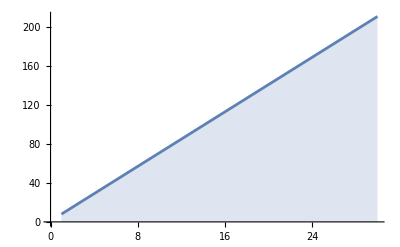

```mathematica
ListLinePlot[Table[combinatorSize[intToBinary[0,d]],{d,1,30}],Filling -> Axis]
```

Number of integers we can represent as d  increases:

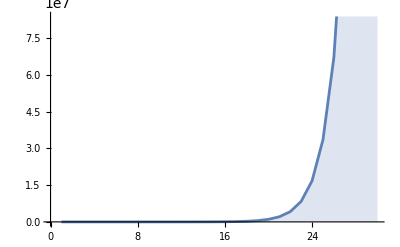

```mathematica
ListLinePlot[Table[{d,Power[2,d]},{d,1,30}],Filling -> Axis]
```

Combinator size as n,  the number it represents, grows:

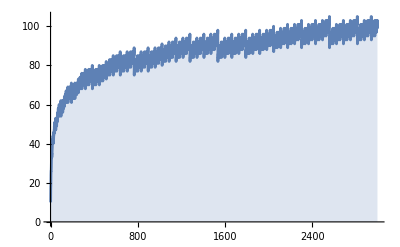

```mathematica
ListLinePlot[Table[combinatorSize[intToBinary[n,Floor[Log2[n]]+1]],{n,1,3000}],Filling -> Axis]
```

Binary numerals can represent integers efficiently because their combinator size is log_2(the number it represents). To represent 10^9, it only needs a combinator of size of 211:

```mathematica
combinatorSize[intToBinary[n,Floor[Log2[1000000000]]+1]]
```

211

Let’s compare with the Church numeral representation:

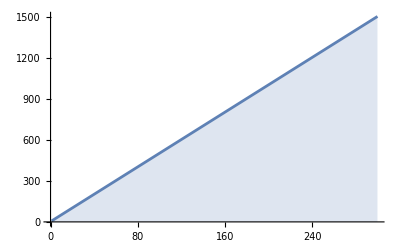

```mathematica
ListLinePlot[Table[combinatorSize[intToChurch[n]],{n,1,300}],Filling -> Axis]
```

It can be seen that to represent 300, the Church numeral has size 1502. Therefore, the binary numeral is much more efficient in representation.

#### Bitwise Operations

Since all bitwise operations are compiled in a similar way, let’s take only an example of the binary and:

Combinator size as d increases:

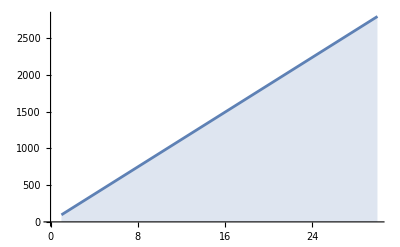

```mathematica
ListLinePlot[Table[combinatorSize[binaryAnd[d]],{d,1,30}],Filling -> Axis]
```

Line of best fit:

```mathematica
pts= Table[{d,combinatorSize[binaryAnd[d]]},{d,1,30}];
```

```mathematica
fit = Fit[pts,{d,1},d]
```

3.+93. d

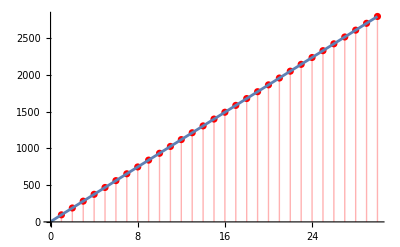

```mathematica
Show[ListPlot[pts,PlotStyle->Red,Filling -> Axis],Plot[{fit},{x,0,30}]]
```

The formula for the size of the binary and combinator is:

```mathematica
fit = Fit[pts,{d,1},d]
```

-4543.67+943. d

where d is its length of binary numerals.

The size complexity of other bitwise combinators can be found in the exactly the same way.

#### Addition

As we previously stated, the size of the addition combinator in binary numerals has a complexity of O(d^2). Let’s visualize it through the line of best fit and linearization:

Visualize the size of the binary addition combinator as d increases:

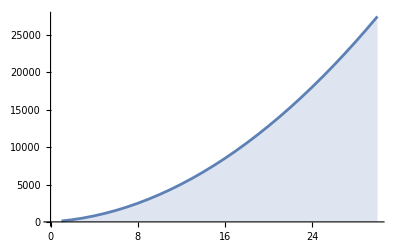

```mathematica
ListLinePlot[Table[combinatorSize[binaryPlus[x]],{x,1,30}],Filling -> Axis]
```

Line of best fit:

```mathematica
pts = Table[{d,combinatorSize[binaryPlus[d]]},{d,1,30}];
```

```mathematica
fit = Fit[pts,{x^2,x,1},x]
```

3.+90.5 x+27.5 x^2

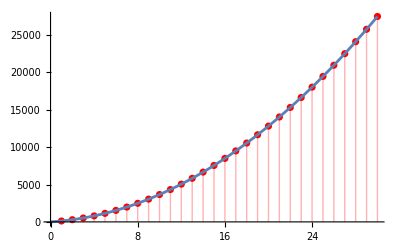

```mathematica
Show[ListPlot[pts,PlotStyle->Red,Filling -> Axis],Plot[{fit},{x,0,30}]]
```

```mathematica
pts = Table[{d,combinatorSize[binaryPlus[d]]},{d,1,30}];
```

```mathematica
fit = Fit[pts,{d^2},d]
```

31.2157 d^2

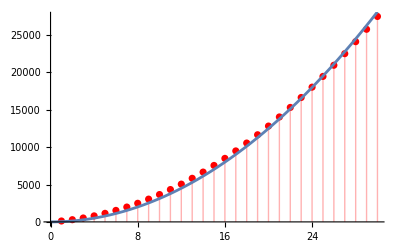

```mathematica
Show[ListPlot[pts,PlotStyle->Red,Filling -> Axis],Plot[{fit},{d,0,30}]]
```

Linearize:

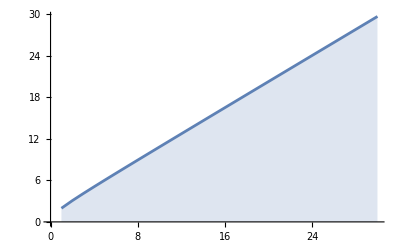

```mathematica
ListLinePlot[Table[Sqrt[combinatorSize[binaryPlus[d]]/31.2157],{d,1,30}],Filling -> Axis]
```

Therefore, the formula for the size of the addition combinator in binary numerals is:

```mathematica
fit = Fit[pts,{d^2},d]
```

31.2157 d^2

where  is the length of the binary numeral.

### Steps to the Fixed Point in Arithmetic

To show the number of steps to the fixed point, we will perform addition with both the binary and Church numerals.

Visualize the evolution of the binary plus combinator:

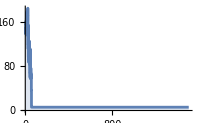
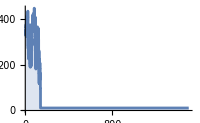
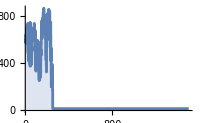
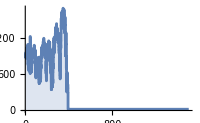
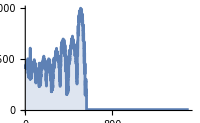
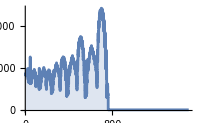
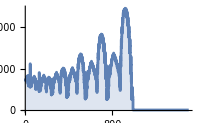
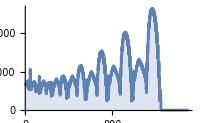

```mathematica
Row[Table[ListStepPlot[combinatorSize/@ResourceFunction["CombinatorEvolveList"][binaryPlus[d][intToBinary[0,d]][intToBinary[0,d]],1500],Filling->Axis,ImageSize->200],{d,1,10}],"     "]
```

Depth plot:

```mathematica
Magnify[Row[Table[ResourceFunction["CombinatorEvolutionPlot"][ResourceFunction["CombinatorFixedPointList"][binaryPlus[d][intToBinary[0,d]][intToBinary[0,d]]],"ExpressionDepthPlot"],{d,1,10}],"     "],2]
```

-Graphics-

Formulating the number of steps to the fixed point:

```mathematica
binaryPts = Table[{d, stepsToFixPoint[binaryPlus[d][intToBinary[0,d]][intToBinary[0,d]]]},{d,1,10}]
```

{{1,57},{2,140},{3,252},{4,393},{5,563},{6,762},{7,990},{8,1247},{9,1533},{10,1848}}

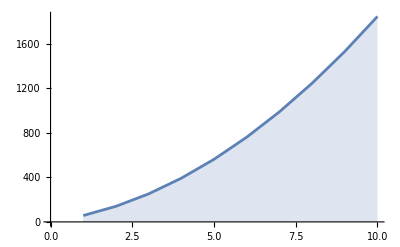

```mathematica
ListLinePlot[Table[x[[2]],{x,binaryPts}],Filling -> Axis]
```

```mathematica
binaryFit = Fit[binaryPts,{d^2,d,1},d]
```

3.+39.5 d+14.5 d^2

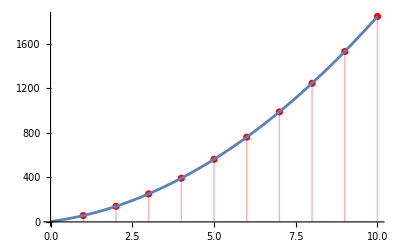

```mathematica
Show[ListPlot[binaryPts,PlotStyle->Red,Filling -> Axis],Plot[{binaryFit},{d,0,10}]]
```

```mathematica
binaryFit = Fit[binaryPts,{d^2},d]
```

19.2623 d^2

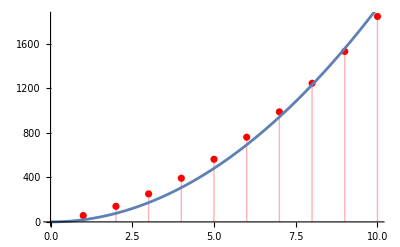

```mathematica
Show[ListPlot[binaryPts,PlotStyle->Red,Filling -> Axis],Plot[{binaryFit},{d,0,10}]]
```

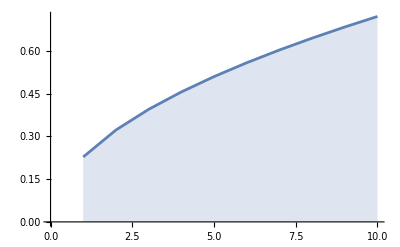

```mathematica
ListLinePlot[Table[Sqrt[binaryPts[d][[1]]/19.2623],{d,1,10}],Filling -> Axis]
```

It doesn’t perfectly fit with the square model; however, it tends to be squared if d gets bigger.

Visualize the relationship between the number of integers it can represent and its number of steps to the fixed point for binary numeral:

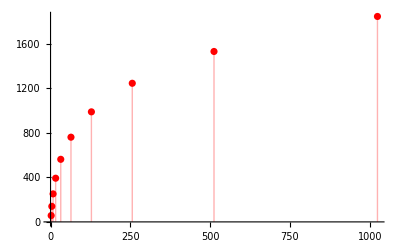

```mathematica
ListPlot[Table[{Power[2,x],binaryPts[[x]][[2]]},{x,1,10}],PlotStyle->Red,Filling -> Axis]
```

Visualize the relationship between the number of integers it can represent and its number of steps to the fixed point for Church numeral:

```mathematica
churchPts = Table[{x,stepsToFixPoint[plus[intToChurch[1]][intToChurch[x-1]][CombinatorS][CombinatorK]]},{x,1,10}];
```

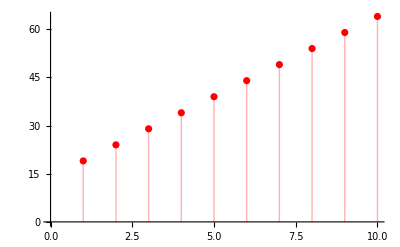

```mathematica
ListPlot[churchPts,PlotStyle->Red,Filling -> Axis]
```

Comparison:

```mathematica
churchFit = Fit[churchPts,{x,1},x]
```

14.+5. x

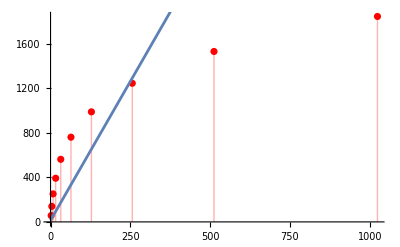

```mathematica
Show[ListPlot[Table[{Power[2,x],binaryPts[[x]][[2]]},{x,1,10}],PlotStyle->Red,Filling -> Axis],Plot[{churchFit},{x,0,1000}]]
```

We can easily see the trends. For Church numerals, the number of steps to the fixed point is proportional to the output result, which is linear. For the binary numerals, it tends to be a curve, which is logarithmic: the greater the integer, the slower the number of steps to the fixed point increases. In the beginning before the intersection point, such that the integer they represent is smaller than about 250, the Church numeral is faster than the binary numeral to reach the fixed point. However, to represent numbers after the intersection point, the binary numeral is much more efficient than the Church numeral.

## Conclusion

This project extensively explored the application of SK combinators in performing arithmetic operations on Church numerals and identifies several more efficient combinators. It is proven that combinators for arithmetic operations, particularly addition, multiplication, and exponentiation, found by Stephen are optimal in both size and the number of steps to the fixed point. However, I also found one combinator for addition and three combinators for exponentiation that are very close to the efficiency of the ones Stephen Wolfram found. By swapping the positions of parameters, a more efficient combinator for exponentiation, S K K, which looks same as the identity combinator, was found.

Additionally, the number of steps to the fixed point for these arithmetic operations, particularly addition, multiplication, and exponentiation, is determined to be proportional to their output value, which is linear. This is because they are built on the successor, which means that each operation builds upon repeated incrementation from an initial value, resulting in the overall complexity scaling linearly with the size of the output. 

Furthermore, this project also introduced a novel approach for constructing SK combinators for binary representations of arbitrary lengths and performing bitwise operations. It is built that is able to be converted between Church numerals and integers. The efficiency and performance of this method to represent integers and performing the basic arithmetic operation, addition, was rigorously compared, revealing that this binary numeral is much more efficient than the Church numeral at scale: its combinator size and the number of steps to reach the fixed point grows logarithmically as n, the number it represents, grows, whereas the Church numeral grows linearly.

### Future Directions

The size and time complexity for the binary representation I constructed to perform addition is proven to be O(d^2), where  is its number of binary digits. However, adding on the constant coefficient, the actual size and time complexity are roughly about O(31.2157 d^2) and O(19.2623 d^2) respectively. In the future works, I want to find optimal combinators, the one with smaller or smallest coefficient for size and timing, for this binary representation.

## Citations

Gustafson, H and Stocke, J. (2023, January 27). Sub-axiomatic foundations of group theory in SK combinators. https://community.wolfram.com/groups/-/m/t/2818259

Paul, E. (2020). Analyzing and computing with combinators. https://community.wolfram.com/groups/-/m/t/2034214

Wikimedia Foundation. (2024, June 16). Church encoding. Wikipedia. https://en.wikipedia.org/wiki/Church_encoding

Wikimedia Foundation. (2024b, July 6). Lambda calculus. Wikipedia. https://en.wikipedia.org/wiki/Lambda_calculus

Wikimedia Foundation. (2024c, July 6). Ski combinator calculus. Wikipedia. https://en.wikipedia.org/wiki/SKI_combinator_calculus

Wolfram, S. (1970, January 1). Note (D) for Universality in Turing machines and other systems: A new kind of science: Online by Stephen Wolfram [page 1121]. Wolfram Science and Stephen Wolfram’s “A New Kind of Science.” https://www.wolframscience.com/nks/notes-11-12--combinators/

Wolfram, S (2020, December). Combinators: A Centennial View. https://writings.stephenwolfram.com/2020/12/combinators-a-centennial-view/#updating-schemes-and-multiway-systems

## Acknowledgements

I would like to express my deepest gratitude to my mentor, Henry Gustafson, for his invaluable guidance and support throughout this project. Special thanks to directors Rory, Megan, and Eryn for their leadership and encouragement. I am also profoundly grateful to Stephen Wolfram for orienting my project and inspiring my research. Thank you to everyone who supported me along the way.